### Simplex Plot

```mathematica
(* Geometric transformation to simplex *)
{err,trans}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
(* Edges of simplex *)
triangle=Graphics[{Thickness[0.005],Darker[Gray],GeometricTransformation[Line[{{0,0},{0,1},{1,0},{0,0}}],trans]}];
(* Some random data *)
dummyData=Select[RandomReal[1,{100,2}],Total[#]<=1&];
(* Plot the points *)
points=ListPlot[dummyData,PlotStyle->PointSize[0.03]];
(* Or plot the lines *)
lines=ListLinePlot[dummyData,PlotStyle->Black];
(* Show all together *)
(* The trick is to extract the "First" part of the plots, and transform it *)
```

## Data processing

```mathematica
SetDirectory[NotebookDirectory[]<>"simulation_data/"]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/fig3_new/simulation_data

```mathematica
filenames=FileNames[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/fig3_new

```mathematica
filenames
```

{3m_c0.00.csv,3m_c0.05.csv,3m_c0.10.csv,3m_c0.15.csv,3m_c0.20.csv,3m_c0.25.csv,3m_c0.30.csv,3m_c0.35.csv,3m_c0.40.csv,3m_c0.45.csv,3m_c0.50.csv,3m_c0.55.csv,3m_c0.60.csv,3m_c0.65.csv,3m_c0.70.csv,3m_c0.75.csv,3m_c0.80.csv,3m_c0.85.csv,3m_c0.90.csv,3m_c0.95.csv,3m_c1.00.csv}

```mathematica
raw3mdata=Table[Import[NotebookDirectory[]<>"simulation_data/"<>ToString[filenames⟦i⟧],"CSV"],{i,1,Length[filenames],1}];
```

```mathematica
raw3mdata//Dimensions
```

{21,1275,4}

```mathematica
raw3mdata⟦1⟧⟦1;;10⟧
```

{{h,l,h_eq,l_eq},{0.,1.,0.,1.},{0.,0.979592,0.,0.62},{0.,0.959184,0.,0.48},{0.,0.938776,0.,0.3},{0.,0.918367,0.,0.2},{0.,0.897959,0.,0.22},{0.,0.877551,0.,0.12},{0.,0.857143,0.,0.06},{0.,0.836735,0.,0.02}}

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

## Analytics

```mathematica
α=0.8;β=2;γ=.;u=0;
q1=2;q2=2.5;q3=3;
p[γ_,y_,q_]:=(1-γ)q/(q1+q2+q3)+α γ (y^β/(y^β+(1-y)^β));
```

```mathematica
gammas=ReplacePart[Table[i,{i,0,1,0.05}],21->0.99]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,0.99}

```mathematica
internal={};
notransinternal={};
Table[
dy1[y1_,y2_]:=y1((p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
dy2[y1_,y2_]:=y2 ((p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
y1=.;
y2=.;
sol=NSolve[{dy1[y1,y2]==0,dy2[y1,y2]==0},{y1,y2},Reals];
data={y1,y2}/.sol;
relData=Select[data,#⟦1⟧>0&&#⟦2⟧>0&&Total[#]<1.&&Total[#]>0&];
AppendTo[internal,{γ,If[relData=={},Missing[],trans[relData⟦1⟧]]}];
AppendTo[notransinternal,{γ,If[relData=={},Missing[],relData⟦1⟧]}];,{γ,gammas}
];
```

```mathematica
internal⟦All,1⟧⟦{7,11,15,19}⟧
```

{0.3,0.5,0.7,0.9}

```mathematica
relData
```

{{0.364143,0.330582},{0.364143,0.330582}}

```mathematica
internal⟦All,2⟧
```

{Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],{0.610274,1.43441×10^-13},{0.591299,0.0441966},{0.577408,0.102845},{0.56708,0.141019},{0.558631,0.168298},{0.551431,0.188966},{0.545159,0.205271},{0.539621,0.218523},{0.534681,0.229542},{0.530243,0.238871},{0.526229,0.246887},{0.52258,0.253858},{0.519247,0.259983},{0.516781,0.264376}}

```mathematica
tlp=TernaryListPlot[{0.3,0.3,0.3},(*AxesStyle->cols⟦{1,3,2}⟧, Axes->True,*)FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,FrameStyle->Thickness[0.005]]
```

-Graphics-

```mathematica
inteqdyn=Show[tlp,ListPlot[internal⟦All,2⟧,Joined->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.005]],Mesh->All,MeshStyle->Directive[PointSize[Medium],Black]],
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]]
```

-Graphics-

## Connecting to data

```mathematica
diamond=Graphics[{Black,Rotate[Rectangle[],45Degree]}];
```

```mathematica
dataplots=Table[Show[Graphics[{EdgeForm[{Black,Thin}],Table[{Blend[cols,{raw3mdata⟦j,2;;⟧⟦i⟧⟦4⟧,1-raw3mdata⟦j,2;;⟧⟦i⟧⟦3⟧-raw3mdata⟦j,2;;⟧⟦i⟧⟦4⟧,raw3mdata⟦j,2;;⟧⟦i⟧⟦3⟧}],RegularPolygon[trans[{raw3mdata⟦j,2;;⟧⟦i⟧⟦2⟧,1-raw3mdata⟦j,2;;⟧⟦i⟧⟦2⟧-raw3mdata⟦j,2;;⟧⟦i⟧⟦1⟧}],{0.01,11},6]},{i,1,Length[raw3mdata⟦j,2;;⟧]}]},Frame->False,PlotRange->{{-0.05,1.05},{-0.05,(√3)/2+0.05}}],ListPlot[{internal⟦All,2⟧⟦j⟧},Joined->True,Axes->False,PlotMarkers->{diamond,Scaled[0.05]}],tlp],{j,1,Length[filenames],1}];
```

```mathematica
cols
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

```mathematica
(*dataplots=Table[Show[triangle,ListPlot[datatransformedlist⟦i⟧,InterpolationOrder->2,PlotStyle->PointSize[Medium],Axes->False,AspectRatio->1],ListPlot[{internal⟦All,2⟧⟦i⟧},Joined->True,Axes->False,PlotMarkers->{◆,Scaled[0.05]}]],{i,1,Length[filenames],1}];*)
```

```mathematica
internal⟦All,1⟧
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,0.99}

```mathematica
Manipulate[{dataplots⟦i⟧,internal⟦All,1⟧⟦i⟧},{i,1,Length[dataplots],1}]
```

```mathematica
ListAnimate[dataplots,ImageSize->Small]
```

```mathematica
triangle=Graphics[{Thickness[0.005],Darker[Gray],Line[{{0,0},{1,0},{1/2,(√3)/2},{0,0}}]}];
```

```mathematica
(*Define the triangle vertices in 2D*)
v1={1,0}; (*corresponds to {1,0,0}*)
v2={0,0}; (*corresponds to {0,1,0}*)
v3={1/2,Sqrt[3]/2}; (*corresponds to {0,0,1}*)

(*Barycentric to Cartesian conversion function*)
barycentricToCartesian[{x1_,x2_,x3_}]:=x1*v1+x2*v2+x3*v3
```

```mathematica
colorcoords={};
Table[If[x>0&&x<1&&y>0&&y<1&&x+y<1,AppendTo[colorcoords,{x,y,1-x-y}]],{x,0,1,0.02},{y,0,1,0.02}];
```

```mathematica
colchart=Blend[cols,#]&/@colorcoords;
```

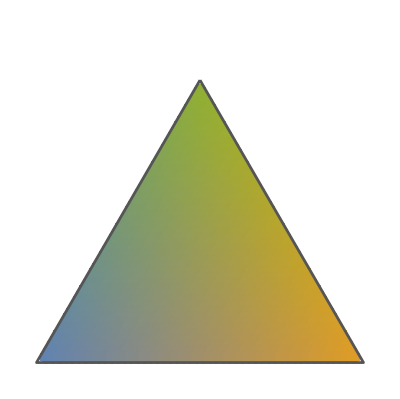

```mathematica
Show[Graphics[{Table[{colchart⟦i⟧,RegularPolygon[barycentricToCartesian[colorcoords⟦i⟧],{0.02,11},6]},{i,1,Length[colorcoords]}]},Frame->False,PlotRange->{0,1}],triangle]
```

## Old

```mathematica
file1=.;
```

```mathematica
transformedlist=Table[Join[trans[{#⟦2⟧,1-#⟦2⟧-#⟦1⟧}],{#⟦3⟧}]&/@raw3mdata⟦i,2;;⟧,{i,1,Length[filenames],1}];
```

```mathematica
plots=Table[Show[triangle,ListDensityPlot[transformedlist⟦i⟧,InterpolationOrder->2,ColorFunction->"SandyTerrain",PlotLegends->Automatic,PlotLayout->{"Row", 2},Frame->False,PlotRange->All,Epilog->Inset[Graphics[Text[ToString[filenames⟦i⟧]]],{0.2,0.7}]]],{i,1,20,1}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
Export[NotebookDirectory[]<>"cdynamics.mov",plots]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/fig3_new/cdynamics.mov

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
coltab=Show[triangle,ListDensityPlot[transformedlist⟦20⟧,InterpolationOrder->2,ColorFunction->#,PlotLegends->Automatic,PlotLayout->{"Row", 2},Frame->False,PlotRange->All,Epilog->Inset[Graphics[Text[ToString[#]]],{0.2,0.7}]]]&/@ColorData["Gradients"];
```

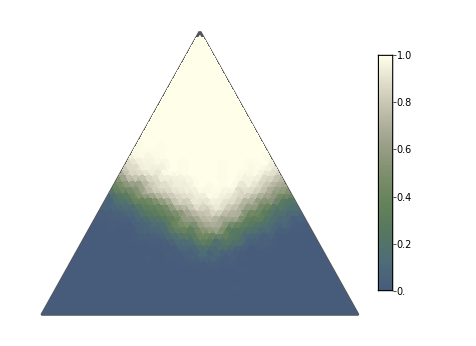
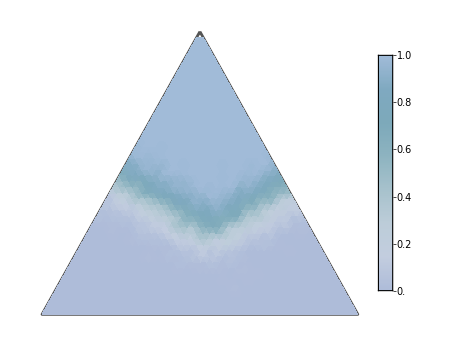
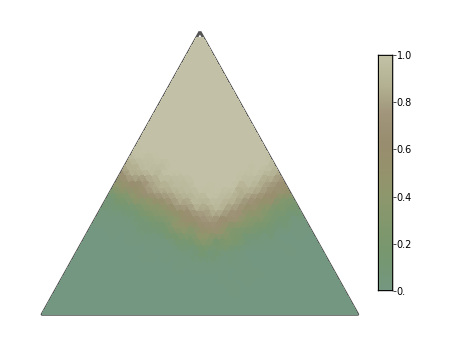
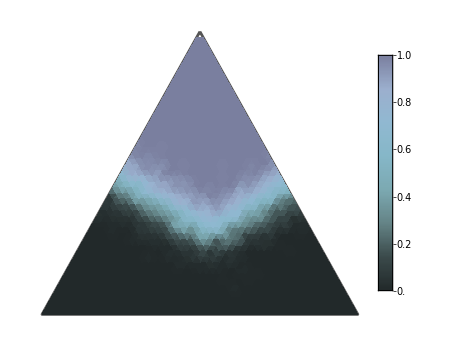
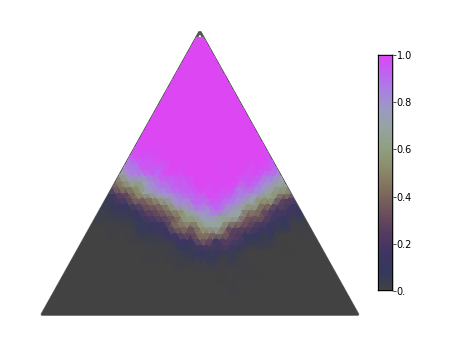
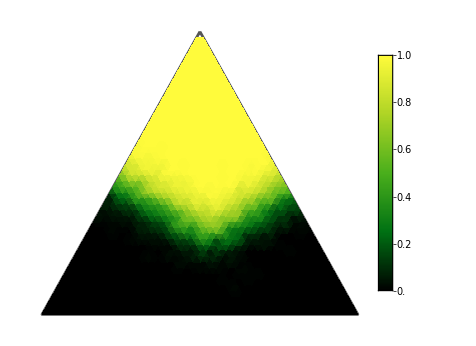
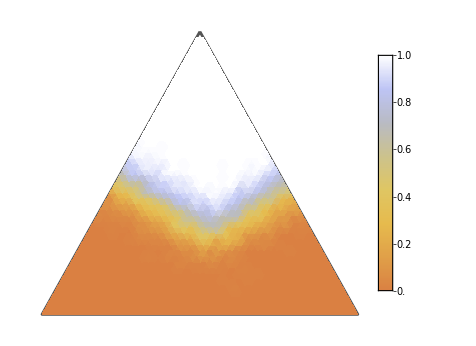
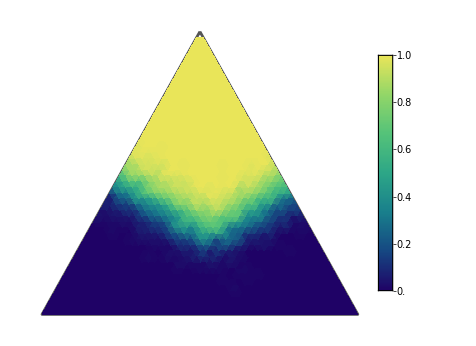

```mathematica
coltab
```

## Dynamic γ

```mathematica
G=0.4;
```

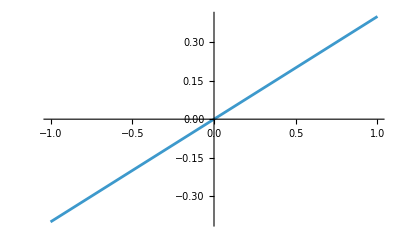

```mathematica
Plot[G y,{y,-1,1}]
```

```mathematica
dy1[y1_,y2_,γ_]:=y1((p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
dy2[y1_,y2_,γ_]:=y2 ((p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
```

```mathematica
sol=NDSolve[{y1'[t]==dy1[y1[t],y2[t],g[t]],y2'[t]==dy2[y1[t],y2[t],g[t]],(*g evolves according to dg*)g'[t]==G Sign[dy1[y1[t],y2[t],g[t]]],(*initial conditions*)y1[0]==0.45,y2[0]==0.5,g[0]==0},{y1,y2,g},{t,0,100}]
```

{{y1→InterpolatingFunction[…],y2→InterpolatingFunction[…],g→InterpolatingFunction[…]}}

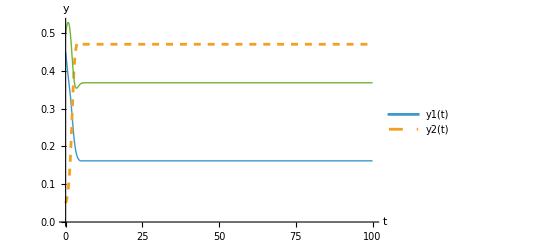

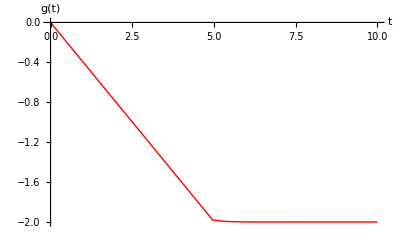

-Graphics-

```mathematica
(*Plot y1 and y2 together*)Plot[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/. sol],{t,0,100},PlotLegends->{"y1(t)","y2(t)"},PlotStyle->{Thick,Dashed},AxesLabel->{"t","y"}]

(*Plot g separately*)
Plot[Evaluate[g[t]/. sol],{t,0,10},PlotStyle->{Thick,Red},AxesLabel->{"t","g(t)"}]

TernaryListPlot[Table[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/. sol]⟦1⟧,{t,0,100,0.01}],Joined->True,(*AxesStyle->cols⟦{1,3,2}⟧, Axes->True,*)PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧]
```

```mathematica
Table[Evaluate[{y1[t],y2[t],1-y1[t]-y2[t]}/. sol],{t,0,100,0.01}]
```

```mathematica
notransinternal
```

{{0.,Missing[]},{0.05,Missing[]},{0.1,Missing[]},{0.15,Missing[]},{0.2,Missing[]},{0.25,Missing[]},{0.3,Missing[]},{0.35,{0.610274,0.389726}},{0.4,{0.565782,0.383184}},{0.45,{0.51803,0.363214}},{0.5,{0.485662,0.351503}},{0.55,{0.461464,0.344202}},{0.6,{0.442331,0.33947}},{0.65,{0.426646,0.336328}},{0.7,{0.413456,0.334215}},{0.75,{0.402155,0.332793}},{0.8,{0.39233,0.331845}},{0.85,{0.383689,0.331231}},{0.9,{0.376015,0.330855}},{0.95,{0.369146,0.330652}},{0.99,{0.364143,0.330582}}}

```mathematica
TernaryListPlot[Table[{notransinternal⟦i,2,1⟧,1-notransinternal⟦i,2,1⟧-notransinternal⟦i,2,2⟧,notransinternal⟦i,2,2⟧},{i,1,Length[notransinternal]}],(*AxesStyle->cols⟦{1,3,2}⟧, Axes->True,*)PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧]
```

Part::partw: Part 1 of Missing[] does not exist.

Part::partw: Part 2 of Missing[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-